## Shortlisting

```mathematica
qm := UniformDistribution[{0,1}]
qf:= UniformDistribution[{0,1}]
maxqm := OrderDistribution[{qm,nm},nm]
maxqf := OrderDistribution[{qf,nf},nf]
Urm:=TransformedDistribution[q,q\[Distributed] qm]
Urf:=TransformedDistribution[b*q,q\[Distributed]qf]
Sm :=OrderDistribution[{Urm, nm},nm]
Sf :=OrderDistribution[{Urf, nf},nf]
```

```mathematica
FSm := CDF[Sm, s]
FSm
```

Piecewise[{{-0^nm+s^nm, 0<s<1}, {1, s≥1}, {0, True}}]

```mathematica
fsf := CDF[Sf, s]
fsf
```

Piecewise[{{(s/b)^nf, 0≤s≤b}, {1, s>b}, {0, True}}]

### Probability that a male is shortlisted

```mathematica
g:= Simplify[(1-FSm)*fsf, Assumptions->0<s<1 && b≥ s && nm>0]
g
```

-(s/b)^nf (-1+s^nm)

```mathematica
prmsl := Simplify[Probability[x>y,{x\[Distributed]Sm, y\[Distributed]Sf}], Assumptions-> b≥1]
prmsl
```

(b^-nf nm)/(nf+nm)

```mathematica
prfsl := Simplify[Probability[y>x,{x\[Distributed]Sm, y\[Distributed]Sf}], Assumptions-> b≥ 1]
prfsl
```

Piecewise[{{(b^nm nf)/(nf+nm), b≤1}, {1-(b^-nf nm)/(nf+nm), True}}]

### Quality of Shortlisted Male

```mathematica
pdfUtilShortlistM := Simplify[PDF[Sm,x]*CDF[Sf,x]/prmsl,Assumptions->0<x<1 &&b>1]
pdfUtilShortlistM
Integrate[x*pdfUtilShortlistM,{x,0,1}]
```

((nf+nm) x^(-1+nf+nm))/(nm Beta[nm,1])

ConditionalExpression[(nf+nm)/(1+nf+nm), Re[nf+nm]>-1]

```mathematica
(*check its correct*)
Simplify[Expectation[x\[Conditioned]x>y, {x\[Distributed]Sm, y\[Distributed]Sf}], Assumptions->b>1 && nm>0 &&nf>0]
```

(nf+nm)/(1+nf+nm)

### Quality of Shortlisted Female

```mathematica
(*pdf of utility from shortlisted female*)
pdfUtilShortlistF := Simplify[PDF[Sf,x]*CDF[Sm,x]/(1-prmsl),Assumptions->0≤ x≤  b &&b>1 && nm ≥ 1&&nf ≥1]
t1 := Integrate[x*Simplify[pdfUtilShortlistF, Assumptions->x<1], {x,0,1}]
t2 := Integrate[x*Simplify[pdfUtilShortlistF, Assumptions->x>1], {x,1,b}]
```

```mathematica
pdfUtilShortlistF
```

(nf (nf+nm) x^(-1+nf) (Piecewise[{{x^nm, 0<x<1}, {1, x≥1}, {0, True}}]))/(-nm+b^nf (nf+nm))

```mathematica
expUtilShortlistF := Simplify[t1+t2, Assumptions->b≥ 1 && nm≥ 1 && nf≥ 1]
expUtilShortlistF
```

(nf (nf+nm) (-nm+b^(1+nf) (1+nf+nm)))/((1+nf) (1+nf+nm) (-nm+b^nf (nf+nm)))

```mathematica
(*check its correct*)
Simplify[Expectation[x\[Conditioned]x>y, {x\[Distributed]Sf, y\[Distributed]Sm}], Assumptions->b≥1 && nm≥ 1 &&nf≥ 1]
```

(nf (nf+nm) (-nm+b^(1+nf) (1+nf+nm)))/((1+nf) (1+nf+nm) (-nm+b^nf (nf+nm)))

```mathematica
(*CDF of utility of shortlisted female*)
cdfUtilShortlistF = Simplify[PDF[Sf,x]*CDF[Sm,x]/(1-prmsl),Assumptions->0<x<b &&b>x]
```

(nf (nf+nm) x^(-1+nf) (Piecewise[{{1, x≥1}, {-0^nm+x^nm, True}}]))/(-nm+b^nf (nf+nm))

### Conditional Probability that male is Hired

```mathematica
DistQualShortlistM := ProbabilityDistribution[pdfUtilShortlistM, {x,0,1}]
(*DistUtilShortlistF := ProbabilityDistribution[pdfUtilShortlistF,{x,0,b}]
DistQualShortlistF := TransformedDistribution[z/b,z\[Distributed]DistUtilShortlistF]
Simplify[PDF[DistQualShortlistF,x], Assumptions->b>x]*)
```

```mathematica
(*PDF of qual of shortlisted female -- change of variable*)
pdfQualShortlistF := With[{x=b*x}, Evaluate[pdfUtilShortlistF]]*D[b*x,x]
pdfQualShortlistF
```

(b nf (nf+nm) (b x)^(-1+nf) (Piecewise[{{(b x)^nm, 0<b x<1}, {1, b x≥1}, {0, True}}]))/(-nm+b^nf (nf+nm))

```mathematica
DistQualShortlistF := ProbabilityDistribution[pdfQualShortlistF, {x,0,1}]
```

```mathematica
probmalehired := Simplify[Probability[x>y, {x\[Distributed]DistQualShortlistM,y\[Distributed]DistQualShortlistF}], Assumptions->nm≥ 1&& nf ≥ 1 &&b>1]
probmalehired
```

(b^(-nf-nm) (nf nm+2 b^(2 nf+nm) (nf+nm)^2-2 b^(nf+nm) nm (2 nf+nm)))/(2 (2 nf+nm) (-nm+b^nf (nf+nm)))

```mathematica
With[{nm=3,nf=1,b=1.7}, Evaluate[probmalehired]]
```

0.651558

```mathematica
Simplify[D[probmalehired,b]]
```

(b^(-1-nf-nm) nf nm (nf+nm) (2 b^(2 nf+nm) nf+nm-b^nf (2 nf+nm)))/(2 (2 nf+nm) (nm-b^nf (nf+nm))^2)

### Total Probability that male is Hired

```mathematica
ProbNMaleSl := BinomialDistribution[2,prmsl]
TotalProbMaleHire := PDF[ProbNMaleSl,1]*probmalehired + PDF[ProbNMaleSl,2]
Simplify[TotalProbMaleHire]
```

(b^(-3 nf-nm) nm (nf nm+2 b^(2 nf+nm) (nf+nm)^2-b^(nf+nm) nm (2 nf+nm)))/((nf+nm)^2 (2 nf+nm))

```mathematica
With[{nm=3,nf=1,b=1.6}, Evaluate[TotalProbMaleHire]]
```

0.536979

```mathematica
(*Derive wrt b*)
DTotalProbMaleHire := Simplify[D[TotalProbMaleHire,b], Assumptions->nm ≥ 1&& nf ≥ 1 && b≥ 1]
DTotalProbMaleHire
```

-(b^(-1-3 nf-nm) nf nm (2 b^(2 nf+nm) (nf+nm)^2-2 b^(nf+nm) nm (2 nf+nm)+nm (3 nf+nm)))/((nf+nm)^2 (2 nf+nm))

```mathematica
Simplify[With[{nm=3,nf=1}, Evaluate[D[TotalProbMaleHire,b]]]]
```

-(3 (9-15 b^4+16 b^5))/(40 b^7)

```mathematica
DTotalProbMaleHire= Simplify[D[TotalProbMaleHire,b], Assumptions->nm ≥ 1&& nf ≥ 1 && b≥ 1]
$Assumptions->Flatten[{Thread[{nm,nf,b}≥ 1],Element[{nm, nf},Integers], Element[{b},Reals], nm > nf}]
FullSimplify@Negative[DTotalProbMaleHire]
```

-(b^(-1-3 nf-nm) nf nm (2 b^(2 nf+nm) (nf+nm)^2-2 b^(nf+nm) nm (2 nf+nm)+nm (3 nf+nm)))/((nf+nm)^2 (2 nf+nm))

True→{nm≥1,nf≥1,b≥1,(nm|nf)∈ℤ,b∈ℝ,nm>nf}

Negative[-(b^(-1-3 nf-nm) nf nm (2 b^(2 nf+nm) (nf+nm)^2-2 b^(nf+nm) nm (2 nf+nm)+nm (3 nf+nm)))/((nf+nm)^2 (2 nf+nm))]

(x/b)^nf (Piecewise[{{1, x≥1}, {-0^nm+x^nm, True}}])

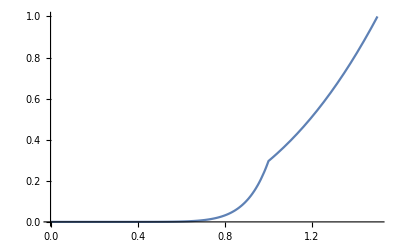

```mathematica
Simplify[F, Assumptions->0<x<b &&b>1]
Plot[With[{nm=7,nf=3,b=1.5}, Evaluate[Simplify[F, Assumptions->0<x<b &&b>1]]],{x,0,1.5}]
```

```mathematica
Ff := Simplify[F, Assumptions->0<x<b && b>x]
Ff
```

(x/b)^nf (Piecewise[{{1, x≥1}, {-0^nm+x^nm, True}}])

((nf+nm) x^(-1+nf+nm))/(nm Beta[nm,1])

ConditionalExpression[(nf+nm)/(1+nf+nm), Re[nf+nm]>-1]

(nf (nf+nm) x^(-1+nf) (Piecewise[{{1, x≥1}, {-0^nm+x^nm, True}}]))/(-nm+b^nf (nf+nm))

```mathematica
Simplify[Integrate[Simplify[(1-FSm)*fsf, Assumptions->0<s<1 && b≥ s], {s,0,1}]]
```

0.296296 x^10

ConditionalExpression[(b^-nf nm)/(nf+nm), Re[nf]>0&&Re[nm]>0]

```mathematica
ConditionalExpression[(b^-nf nm)/(nf+nm), Re[nf]>0&&Re[nm]>0]
```

```mathematica
prmsl := Simplify[Probability[x>y,{x\[Distributed]Sm, y\[Distributed]Sf}], Assumptions-> b>1]
prmsl
```

(b^-nf nm)/(nf+nm)

```mathematica
g := Simplify[Integrate[Simplify[(1-FSm)*fsf, Assumptions->0<s<1 && b≥ s], s]]
g
```

```mathematica
prmsl
```

((c/(b+c))^nf nm)/(nf+nm)

```mathematica
With[{c=2, b=0.5, nm=7, nf=3},Evaluate[prmsl]]
```

0.3584

```mathematica
condexputilm := Simplify[Expectation[x\[Conditioned]x>y, {x\[Distributed]Sm, y\[Distributed]Sf}], Assumptions-> b >1]
condexputilm
```

(nf+nm)/(1+nf+nm)

```mathematica
With[{nm=7, nf=3,b=1.5},Evaluate[condexputilm]]
```

10/11

```mathematica
condexputilf := Simplify[Expectation[y\[Conditioned]y>x, {x\[Distributed]Sm, y\[Distributed]Sf}], Assumptions->b>1]
condexputilf
```

(nf (nf+nm) (-nm+b^(1+nf) (1+nf+nm)))/((1+nf) (1+nf+nm) (-nm+b^nf (nf+nm)))

```mathematica
With[{nm=7,nf=3,b=1.5},Evaluate[condexputilf]]
```

1.24097

```mathematica
exputil := (prmsl*condexputilm) + ((1-prmsl)*condexputilf)
Simplify[exputil]
```

(b nf+(b^-nf nm)/(1+nf+nm))/(1+nf)

```mathematica
With[{nm=7, nf=3,b=1.5},Evaluate[exputil]]
```

1.17214

```mathematica
OrderDistribution[{Urm, nm},nm]
```